```mathematica
Exit[]
```

```mathematica
Eklipse=23.5;
```

```mathematica
Sonne[Breite_,Tage_]:={{1,0,0},{0,Sin[Breite °],-Cos[Breite °]},{0,Cos[Breite °],Sin[Breite °]}}.{Cos[(π Tage)/180] Cos[2 π Tage]-Cos[° Eklipse] Sin[(π Tage)/180] Sin[2 π Tage],Cos[° Eklipse] Cos[2 π Tage] Sin[(π Tage)/180]+Cos[(π Tage)/180] Sin[2 π Tage],Sin[° Eklipse] Sin[(π Tage)/180]}
```

```mathematica
Winkel[b_,t_]:=180/Pi{ArcCos[Sonne[b,t][[1]]/(Sonne[b,t][[1]]^2+Sonne[b,t][[2]]^2)],ArcSin[Sonne[b,t][[3]]]}
```

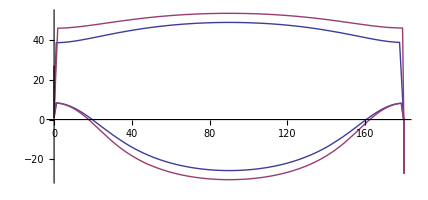

```mathematica
m=13;ParametricPlot[{Winkel[52.5,t+m*30],Winkel[47.9,t+m*30]},{t,0,1},PlotRange->All]
```

```mathematica
m=10;ParametricPlot3D[{Sonne[52.5,t],Sonne[47.9,t]},{t,m*30,m*30+1}]
```

-Graphics3D-